Problem 1

```mathematica
A = Table[1/(i^2+2j^2),{i,1,4},{j,1,4}];
u = {1,0,-1,1};
x= {x1,x2,x3,x4};
Solve[A.x == u,x]
```

{{x1→-1145133/11200,x2→1319013/700,x3→-555536421/78400,x4→16061463/2450}}

Problem 2 (a)(b)(c)

```mathematica
Clear[f,v,x,h]
h[x_]:= 1/; x>2
h[x_]:= 0/; x≤ 2
g[y_]:= 1 /; y ∈ Reals
g[y_]:= 0
ρ[v_]:=1 /; VectorQ[v]
ρ[v_]:=0
f[v_]:= True /; ρ[v]== 1 && g[v[[2]]]==1 && h[v[[2]]]==1 
f[v_]:= False

data=Table[{RandomReal[{0,4}],RandomReal[{0,4}]} Exp[I Pi/2 RandomInteger[{0,3}]],{100}];
result = Select[data,f]

Clear[i,j,r]
Dvalue[i_]:=data[[i]];
r={};
Do[If[ f[Dvalue[j]],r=Append[r,Dvalue[j]],0] ,{j,100}]
r
```

{{3.34117,2.71679},{1.50589,2.27689},{2.87955,2.37239},{2.92171,2.41444},{2.06063,3.66393},{0.130632,3.73854},{0.420695,3.07974},{2.04613,2.42717},{1.00636,3.35403},{0.640792,2.89276}}

{{3.34117,2.71679},{1.50589,2.27689},{2.87955,2.37239},{2.92171,2.41444},{2.06063,3.66393},{0.130632,3.73854},{0.420695,3.07974},{2.04613,2.42717},{1.00636,3.35403},{0.640792,2.89276}}

### Problem 3

```mathematica
Solve[{x^2+2y==0, y^2+2x==0},{x,y}]
Solve[{x^2+2y==0, y^2+2x==0},{x,y}]//N
```

{{x→-2,y→-2},{x→0,y→0},{x→2 (-1)^(1/3),y→-2 (-1)^(2/3)},{x→-2 (-1)^(2/3),y→2 (-1)^(1/3)}}

{{x→-2.,y→-2.},{x→0.,y→0.},{x→1.+1.73205 ⅈ,y→1.-1.73205 ⅈ},{x→1.-1.73205 ⅈ,y→1.+1.73205 ⅈ}}

### Problem 4

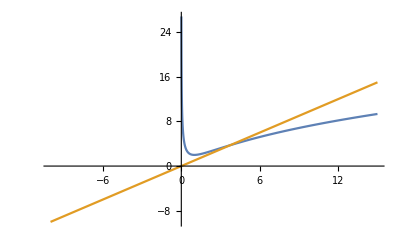

{x→3.73996}

```mathematica
Clear["Global'*"]
Clear[x]
Plot[{Log[x]^2+2,x},{x,-10,15}]
FindRoot[Log[x]^2+2==x,{x,4}]
```

### Newton’s method

```mathematica
Clear[x]
f[x_]=Log[x]^2+2-x ;
x=4.0;nc=0;x0=0;
While[Abs[x-x0]>10^-20 && nc<100,nc=nc+1;x0=x;x= x0-f[x0]/f'[x0]];x
```

0

3.73996

### Problem 5

```mathematica
Clear[x]
Simplify[Integrate[Cos[p x]/(a^2+x^2),{x,-∞,∞}],p∈Reals &&a∈Reals]
```

(ⅇ^(-Abs[a] Abs[p]) π)/Abs[a]

### Problem 6

(1+x) Log[1+x]

x+x^2/2-x^3/6+x^4/12-x^5/20+x^6/30

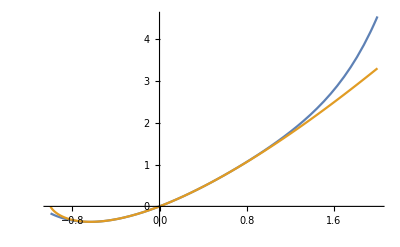

x+x^2/2-x^3/6+x^4/12-x^5/20+x^6/30-x^7/42+x^8/56-x^9/72+x^10/90-x^11/110+x^12/132-x^13/156+x^14/182-x^15/210+x^16/240-x^17/272+x^18/306-x^19/342+x^20/380-x^21/420+x^22/462-x^23/506+x^24/552-x^25/600+x^26/650-x^27/702+x^28/756-x^29/812+x^30/870-x^31/930+x^32/992-x^33/1056+x^34/1122-x^35/1190+x^36/1260-x^37/1332+x^38/1406-x^39/1482+x^40/1560-x^41/1640+x^42/1722-x^43/1806+x^44/1892-x^45/1980+x^46/2070-x^47/2162+x^48/2256-x^49/2352+x^50/2450-x^51/2550+x^52/2652-x^53/2756+x^54/2862-x^55/2970+x^56/3080-x^57/3192+x^58/3306-x^59/3422+x^60/3540-x^61/3660+x^62/3782-x^63/3906+x^64/4032-x^65/4160+x^66/4290-x^67/4422+x^68/4556-x^69/4692+x^70/4830-x^71/4970+x^72/5112-x^73/5256+x^74/5402-x^75/5550+x^76/5700-x^77/5852+x^78/6006-x^79/6162+x^80/6320-x^81/6480+x^82/6642-x^83/6806+x^84/6972-x^85/7140+x^86/7310-x^87/7482+x^88/7656-x^89/7832+x^90/8010-x^91/8190+x^92/8372-x^93/8556+x^94/8742-x^95/8930+x^96/9120-x^97/9312+x^98/9506-x^99/9702+x^100/9900

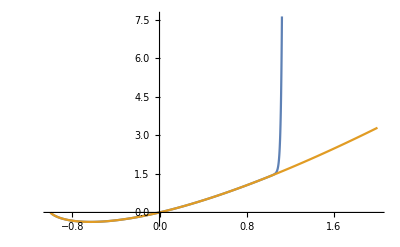

```mathematica
Clear["Global`*"]
f[x_]=(x+1)Log[x+1]
f1[x_]=Series[f[x],{x,0,6}]//Normal
Plot[{f1[x],f[x]},{x,-1,2}]
f1[x_]=Series[f[x],{x,0,100}]//Normal 
Plot[{f1[x],f[x]},{x,-1,2}]
```

### Problem 7(a)

```mathematica
Clear["Global`*"]
data={{1.,2.},{0.,5.},{3.,-1.},{2.,0.}};
f[x_,n_]=x^(n-1);
fn=Table[f[x,n],{n,1,4}];
f0[x_]=Table[f[x,n],{n,1,4}];
A = {f0[1.],f0[0.],f0[3.],f0[2.]};
v = {2.,5.,-1.,0.};
c= {c1,c2,c3,c4};
Solve[A.c == v,c]//Simplify
Fit[data,fn,x]
```

{{c1→5.,c2→-3.5,c3→0.5,c4→-6.5791×10^-17}}

5.-3.5 x+0.5 x^2-5.20568×10^-16 x^3

### Problem 7(b) -Graphics-

### Problem 7(c)

Function and plot get from Fit

0.981133-2.66395 x+2.82557 x^2-1.11501 x^3

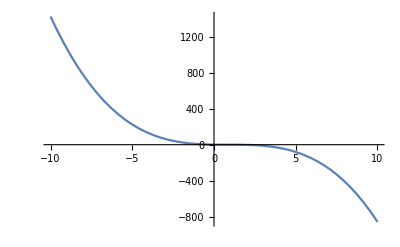

Function and plot get from Solve

{c[1]→0.981133,c[2]→-2.66395,c[3]→2.82557,c[4]→-1.11501}

-Graphics-

```mathematica
Clear["Global`*"]
data=Table[s=RandomReal[];
{s,Exp[-3s]+RandomReal[{-.05,.05}]},{40}];

"Function and plot get from Fit"
r[x_]=Fit[data,{1,x,x^2,x^3},x]//Normal
Plot[r[x],{x,-10,10}]


"Function and plot get from Solve"
g[x_] = c[1] + c[2]x + c[3]x^2 + c[4] x^3;
g[x_] = Sum[c[n] x^(n-1),{n,1,4}];

Dvalue[i_]:=data[[i]];
Xv[i_]:=Dvalue[i][[1]];
Yv[i_]:=Dvalue[i][[2]];

Solve[{Sum[ g[Xv[j]]-Yv[j],{j,1,40}]== 0 ,Sum[  Xv[j](g[Xv[j]]-Yv[j]),{j,1,40}]== 0 ,Sum[( Xv[j]^2)(g[Xv[j]]-Yv[j]),{j,1,40}]== 0 ,Sum[ (Xv[j]^3)(g[Xv[j]]-Yv[j]),{j,1,40}]== 0 },
{c[1],c[2],c[3],c[4]}];
r=Flatten[%]
c[1]=r[[1,2]];
c[2]=r[[2,2]];
c[3]=r[[3,2]];
c[4]=r[[4,2]];
Plot[g[x],{x,-10,10}]
```